```mathematica
Clear[QCTMC];
QCTMC=QueueInit[2,2,"A"];
GovME=GovernMat[QCTMC];
GovM=N[GovME];
t= 10;
```

```mathematica
KryInitTime=List[];
KryInitAcu=List[];
t=10;
Do[
InitState=L2V[QCTMC,RandomInitState[QCTMC,"A"]];
ExactRes=MatrixExp[GovME*t,Flatten[InitState]];
KryRes=AbsoluteTiming[MatrixExp[GovM*t,N[Flatten[InitState]],Method->"Krylov"]];
time=KryRes[[1]];
error=Max[Abs[ExactRes-KryRes[[2]]]];
AppendTo[KryInitTime,{i,time}];
AppendTo[KryInitAcu,{i,error}];
Print[i];
,{i,1,100}]
```

```mathematica
KryInitTime=SortBy[KryInitTime,Last];
```

```mathematica
Time=List[];
Do[
AppendTo[Time,item[[2]]];
,{item,KryInitTime}]
Index=List[];
Do[
AppendTo[Index,item[[1]]];
,{item,KryInitTime}]
```

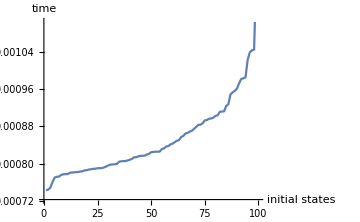

```mathematica
Timeplot=ListLinePlot[Time,AxesLabel->{"initial states", "time"},ImageSize->5*72,BaseStyle->{FontSize->10,FontFamily->"Helvetica"}]
Export["4_4_InitSortTime.eps",First@ImportString[ExportString[Timeplot,"PDF"]]];
```

```mathematica
Export[NotebookDirectory[]<>"EPS_figure\\Initial_states.eps",Timeplot]
```

C:\Users\mei\Desktop\Transient Analysiso of QCTMC\Code\EPS_figure\Initial_states.eps

```mathematica
KryInitAcu=SortBy[KryInitAcu,Last];
Acu=List[];
Do[
AppendTo[Acu,item[[2]]];
,{item,KryInitAcu}]
```

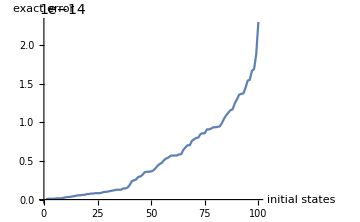

```mathematica
Acuplot=ListLinePlot[Acu,AxesLabel->{"initial states", "exact error"},ImageSize->5*72,BaseStyle->{FontSize->10,FontFamily->"Helvetica"}]
```

```mathematica
Export[NotebookDirectory[]<>"EPS_figure\\Initial_states_arranged.eps",Acuplot]
```

C:\Users\mei\Desktop\Transient Analysiso of QCTMC\Code\EPS_figure\Initial_states_arranged.eps